# SRF Cavity GW Detection Scheme:

## Electromagnetic couplings of cavities with mechanical oscillations induced by gravitational waves

## Constants

```mathematica
(* define all physical constants (not cavity parameters) *)
SPEEDOFLIGHT=1.0(*3.0*10.0^8.0;*);
shearModulus=38.0*10^9;
youngsModulus=105.0*10^9;
matieralDensity=8.57*10^(-3)/((10^(-2))^3);
```

```mathematica
(* define all derived constants *)
lambdaMaterial = -shearModulus*(youngsModulus-2*shearModulus)/(youngsModulus-3*shearModulus);
vt = (matieralDensity/shearModulus)^(-1/2);
vl = (matieralDensity/(lambdaMaterial+2*shearModulus))^(-1/2);
```

```mathematica
(* define all cavity parameters *)
innerRadius=1.0;
outerRadius=1.01;
maxWaveNumber=10.0^3;
```

# Spherical Shell Cavities

## Calculate Resonant Frequencies

### Get Resonant Frequencies

Here we need to numerically determine the resonant frequencies of the spherical shell using the methods from Sebastian’s notes.

```mathematica
(* define small m matrix as a function of either j or y and the radius r *)
smallMmatrix[j1y0_,r_,m_,n_,a_,pmn_,kmn_]:={{(m/(pmn*r) - lambdaMaterial/(2*shearModulus))*If[j1y0==1,SphericalBesselJ[m,pmn*r],SphericalBesselY[m,pmn*r]] - If[j1y0==1,SphericalBesselJ[m+1,pmn*r],SphericalBesselY[m+1,pmn*r]], -((m*(m+1)*((m-1)*If[j1y0==1,SphericalBesselJ[m,kmn*r],SphericalBesselY[m,kmn*r]] - kmn*r*If[j1y0==1,SphericalBesselJ[m+1,kmn*r],SphericalBesselY[m+1,kmn*r]]))/(pmn^2*r^2))},{((m-1)*If[j1y0==1,SphericalBesselJ[m,pmn*r],SphericalBesselY[m,pmn*r]] - pmn*r*If[j1y0==1,SphericalBesselJ[m+1,pmn*r],SphericalBesselY[m+1,pmn*r]])/(pmn^2*r^2),((kmn^2 * r^2*If[j1y0==1,SphericalBesselJ[m+1,kmn*r],SphericalBesselY[m+1,kmn*r]]-(kmn*m*r+m^2+m-2)*If[j1y0==1,SphericalBesselJ[m,kmn*r],SphericalBesselY[m,kmn*r]])/(2*pmn^2*r^2))}};
```

```mathematica
bigMmatrix[m_,n_,a_,outerShell_,innerShell_,pmn_,kmn_]:=Evaluate[ArrayFlatten[{{smallMmatrix[1,outerShell,m,n,a,pmn,kmn],smallMmatrix[0,outerShell,m,n,a,pmn,kmn]},{smallMmatrix[1,innerShell,m,n,a,pmn,kmn],smallMmatrix[0,innerShell,m,n,a,pmn,kmn]}}]]
```

```mathematica
myDeterminant=Simplify[Det[bigMmatrix[m,1,a,b,a,pmn,kmn]]];
matrixMdeterminent[m_,a_,b_,pmn_,kmn_]:=Evaluate[myDeterminant]
Clear[myDeterminant];
```

```mathematica
waveNumbersK=Table[kmn/.Quiet[Solve[{matrixMdeterminent[m,1.0,1.01,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]==0,0≤kmn≤10^3},kmn]],{m,0,2}]//N;
```

```mathematica
waveNumbersKmIs0=waveNumbersK
waveNumbersP=Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)]*waveNumbersK
```

{{314.162,628.32,717.924,942.479},{0.897349,2.31651,3.1262,314.166,628.322,717.932,942.48},{1.78981,5.2182,314.172,628.325,717.946,942.482}}

{{137.476,274.95,314.16,412.424},{0.392675,1.01369,1.36801,137.477,274.95,314.163,412.424},{0.783212,2.28346,137.48,274.952,314.17,412.425}}

```mathematica
vt*Sqrt[waveNumbersK]
```

{{37323.2,52782.7,56421.,64645.3},{1994.72,3204.93,3723.14,37323.4,52782.8,56421.3,64645.4},{2817.12,4810.18,37323.7,52782.9,56421.9,64645.4}}

### Reproduce Fig. (4) from Sebastian’s Notes

```mathematica
matrixDeterminantValues=Table[{m,kmn,Log10[Abs[matrixMdeterminent[m,1.0,1.01,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,0.1,10.0,0.01},{m,0.0,2.0,0.1}]//AbsoluteTiming
```

$Aborted

```mathematica
matrixDeterminantValues2=ArrayFlatten[matrixDeterminantValues[[2]],1];
```

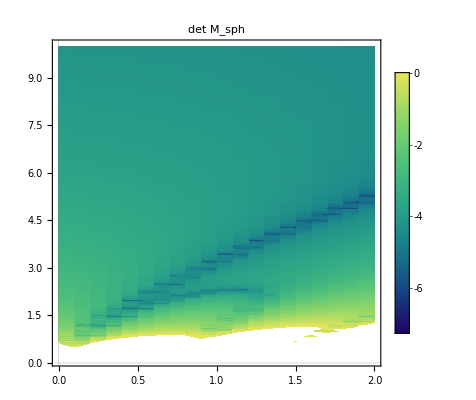

```mathematica
ListDensityPlot[matrixDeterminantValues2,PlotTheme->"Scientific",PlotLabel->"det M_sph",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,InterpolationOrder->4]
```

```mathematica
matrixDeterminantValues=Table[{m,kmn,Log10[Abs[matrixMdeterminent[m,1.0,1.01,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,1.0,1000.0,1.0},{m,0.0,2.0,0.1}]//AbsoluteTiming
```

{36.8705,{{{0.,1.,-1.08566},{0.1,1.,-1.73604},{0.2,1.,-2.34812},{0.3,1.,-1.67943},{0.4,1.,-1.03479},{0.5,1.,-0.708811},{0.6,1.,-0.517751},7,{1.4,1.,0.450862},{1.5,1.,0.492472},{1.6,1.,0.387819},{1.7,1.,-1.36541},{1.8,1.,0.716562},{1.9,1.,1.17155},{2.,1.,1.49037}},998,{1}}}
 |  |  |  |

```mathematica
matrixDeterminantValues2=ArrayFlatten[matrixDeterminantValues[[2]],1];
```

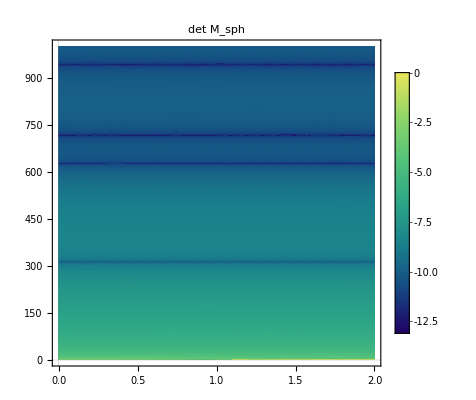

```mathematica
ListDensityPlot[matrixDeterminantValues2,PlotTheme->"Scientific",PlotLabel->"det M_sph",ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,InterpolationOrder->4]
```

### Reproduce Second part of fig (4)

```mathematica
logDeterminantValuesM1=Table[{kmn,Log10[Abs[matrixMdeterminent[1,1.0,1.1,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,0.01,3.0,0.01}];
logDeterminantValuesM2=Table[{kmn,Log10[Abs[matrixMdeterminent[2,1.0,1.1,kmn*Sqrt[shearModulus/(lambdaMaterial+2*shearModulus)],kmn]]]},{kmn,0.01,3.0,0.01}];
```

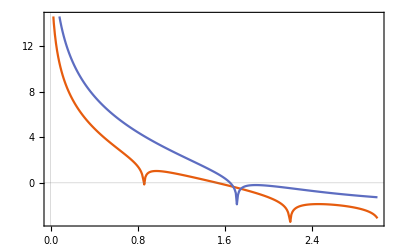

```mathematica
ListPlot[{logDeterminantValuesM1,logDeterminantValuesM2},PlotTheme->"Scientific",Joined->True]
```

### Import Mechanical Modes Data

```mathematica
MODES =Quiet[ToExpression[Quiet[Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/radius1-thickness1percent/NbCavity-r=1.0-1.01.txt"]]]];
```

```mathematica
MODES[[1]][[1]]
```

m2n0l0→{wavenumberk→1.78981,wavenumberp→0.783212,frequency→2817.12,C0→13.4626,C2→0.000448489,D0→0.865461,D2→-0.0103149}

```mathematica
waveNumbersK={{0},{0},Table["wavenumberk"/.(StringJoin["m",ToString[2],"n",ToString[n],"l",ToString[0]]/.MODES[[1]]),{n, 0, 10}]}
waveNumbersP={{0},{0},Table["wavenumberp"/.(StringJoin["m",ToString[2],"n",ToString[n],"l",ToString[0]]/.MODES[[1]]),{n, 0, 10}]}
```

{{0},{0},{1.78981,5.2182,314.172,628.325,717.946,942.482,wavenumberk/.m2n6l0,wavenumberk/.m2n7l0,wavenumberk/.m2n8l0,wavenumberk/.m2n9l0,wavenumberk/.m2n10l0}}

{{0},{0},{0.783212,2.28346,137.48,274.952,314.17,412.425,wavenumberp/.m2n6l0,wavenumberp/.m2n7l0,wavenumberp/.m2n8l0,wavenumberp/.m2n9l0,wavenumberp/.m2n10l0}}

## Define Functions

### Get Bessel function zeros sorted

```mathematica
garbageVariableUsedToDefineFunctions=FullSimplify[D[x*SphericalBesselJ[n,x],x]];
sphericalBesselDerivative[n_,x_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=x*SphericalBesselJ[n,x];
sphericalBessel[n_,x_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

```mathematica
sphericalBesselJZero = Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/bessel-zeros/norm_spherical_bessel_zeros.txt", "CSV"];
sphericalBesselJDerivZero = Import["/Users/wentmich/Documents/uiuc/research/GWs/GWs-Mechanical-Coupling/SphereModes/bessel-zeros/norm_spherical_bessel_derivatives_zeros.txt", "CSV"];
```

```mathematica
SphericalBesselJZero[n_,p_]:=sphericalBesselJZero[[n+1]][[p]]
SphericalBesselJDerivZero[n_,p_]:=sphericalBesselJDerivZero[[n+1]][[p]]
```

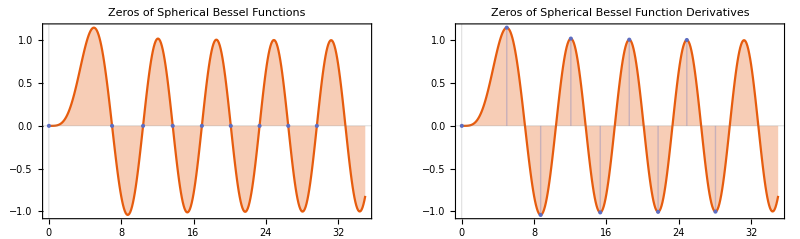

```mathematica
(* plot some of the bessel functions with their zeros *)
whichBessel=3;
bessel0=Table[{x,sphericalBessel[whichBessel,x]},{x,0.0,35,0.1}];
besselZeros=Table[{sphericalBesselJDerivZero[[whichBessel+1,i]],sphericalBessel[whichBessel,sphericalBesselJDerivZero[[whichBessel+1,i]]]},{i,1,Length[sphericalBesselJDerivZero[[whichBessel+1]]]}];
p1 = ListPlot[{bessel0,besselZeros},Joined->{True, False},PlotRange->Full,Filling->{Axis},PlotTheme->"Scientific",PlotLabel->"Zeros of Spherical Bessel Function Derivatives"];
bessel0=Table[{x,sphericalBessel[whichBessel,x]},{x,0.0,35,0.1}];
besselZeros=Table[{sphericalBesselJZero[[whichBessel+1,i]],sphericalBessel[whichBessel,sphericalBesselJZero[[whichBessel+1,i]]]},{i,1,Length[sphericalBesselJZero[[whichBessel+1]]]}];
p2 = ListPlot[{bessel0,besselZeros},Joined->{True, False},PlotRange->Full,Filling->{Axis},PlotTheme->"Scientific",PlotLabel->"Zeros of Spherical Bessel Functions"];
besselGrid = GraphicsGrid[{{p2,p1}}]
```

### Conventions

“parity” --- 1 means even parity and 0 means odd parity
“TMorTE” --- 1 means TM and 0 means TE
The indices here are rather weird. Need to be careful about the selection rules and all that.

SELECTION RULES FOR EM CAVITIES (EVEN)
0 <= m <= n azimuthal
0 <= n inclination
1 <= p radial

SELECTION RULES FOR MECHANICAL CAVITIES
n >= 1 radial
m >= 0 inclination
l <= m azimuthal

### Write down the mechanical modes for a spherical shell

```mathematica
(* wave numbers *)
wavek[m_,n_,l_,a_]:=Inactivate[waveNumbersK[[m+1]][[n+1]]]
wavep[m_,n_,l_,a_]:=Inactivate[waveNumbersP[[m+1]][[n+1]]]
(*wavek[m_,n_,l_,a_]:= Sqrt[omegaMech[m,n,l,a]^2 / vt^2];
wavep[m_,n_,l_,a_]:= Sqrt[omegaMech[m,n,l,a]^2 / vl^2];*)
omegaMech[m_,n_,l_,a_]:=vt*Sqrt[wavek[m,n,l,a]]
(* constituent functions *)
auxϕ[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselJ[m,wavep[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
auxϕT[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselY[m,wavep[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
auxψ[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselJ[m,wavek[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
auxψT[m_,n_,l_,a_,r_,θ_,ϕ_]:=SphericalBesselY[m,wavek[m,n,l,a]*r]*SphericalHarmonicY[m,l,θ,ϕ];
(* mechanical mode displacement vector *)
garbageVariableUsedToDefineFunctions=c0*Grad[auxϕ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"] + d0*Grad[auxϕT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]+c1*Cross[{r,θ,ϕ},Grad[auxψ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]+d1*Cross[{r,θ,ϕ},Grad[auxψT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]+I*c2*Curl[Cross[{r,θ,ϕ},Grad[auxψ[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]],{r,θ,ϕ},"Spherical"]+I*d2*Curl[Cross[{r,θ,ϕ},Grad[auxψT[m,n,l,a,r,θ,ϕ],{r,θ,ϕ},"Spherical"]],{r,θ,ϕ},"Spherical"];
displacementVecQ[m_,n_,l_,a_,c0_,d0_,c1_,d1_,c2_,d2_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

### EM modes from a vector potential

This section draws from chapter (4) of Hill. There, the magnetic displacement field is given instead of B, but if you set c = 1 and use B instead of H, then you should get that the amplitudes of the TM and TE vector potentials are in the same units (both in units of V/m).

```mathematica
(* TE frequencies *)
wavenumberTE[m_,n_,p_,a_]:=Inactivate[SphericalBesselJZero[n,p]]/a
omegaTE[m_,n_,p_,a_]:=SPEEDOFLIGHT*wavenumberTE[m,n,p,a]
(* TM frequencies *)
wavenumberTM[m_,n_,p_,a_]:=Inactivate[SphericalBesselJDerivZero[n,p]]/a
omegaTM[m_,n_,p_,a_]:=SPEEDOFLIGHT*wavenumberTM[m,n,p,a]

(* Transverse electric vector potential *)
vectorPotentialTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:={amplitude*r*SphericalBesselJ[n,Inactivate[SphericalBesselJZero[n,p]]*r/a]*LegendreP[n,m,Cos[θ]]*If[parity==1,Cos[m*ϕ],Sin[m*ϕ]],0,0}
(* Transverse magnetic vector potential *)
vectorPotentialTM[amplitude_,parity_,m_,n_,p_,a_,k_,r_,θ_,ϕ_]:={amplitude*r*SphericalBesselJ[n,Inactivate[SphericalBesselJDerivZero[n,p]]*r/a]*LegendreP[n,m,Cos[θ]]*If[parity==1,Cos[m*ϕ],Sin[m*ϕ]],0,0}
(* calculate electric and magnetic fields for TE modes *)
garbageVariableUsedToDefineFunctions=Evaluate[-Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]];
electricFieldTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=Module[{r0,θ0,ϕ0},Evaluate[(1/k)*Curl[Curl[vectorPotentialTE[amplitude,parity, m,n,p,a,k,r0,θ0,ϕ0],{r0,θ0,ϕ0},"Spherical"],{r0,θ0,ϕ0},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}];
magneticFieldTE[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
(* calculate electric and magnetic fields for TE modes *)
garbageVariableUsedToDefineFunctions=Module[{r0,θ0,ϕ0},Evaluate[(1/k)*Curl[Curl[vectorPotentialTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"],{r,θ,ϕ},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}];
electricFieldTM[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
garbageVariableUsedToDefineFunctions=Module[{r0,θ0,ϕ0},Evaluate[Curl[vectorPotentialTM[amplitude,parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]]/.{r0->r,θ0->θ,ϕ0->ϕ}];
magneticFieldTM[amplitude_,parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Evaluate[garbageVariableUsedToDefineFunctions]
Clear[garbageVariableUsedToDefineFunctions]
```

### Get EM normalization

```mathematica
getNormalizationFactor[parity_,mem_,nem_,pem_,a_,tmorte_,k_]:=Sqrt[((4/3)*Pi*a^2)/NIntegrate[Norm[If[tmorte==1,electricFieldTM[1.0,parity,mem,nem,pem,a,k,r,theta,phi],electricFieldTE[1.0,parity,mem,nem,pem,a,k,r,theta,phi]]]^2*r^2*Sin[theta],{r,0.0,a},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]]
```

### Get energy associated with an electric field configuration

```mathematica
calculateEMFieldEnergy[TMorTE_,amplitude_,parity_,m_,n_,p_,a_,k_]:=(1/2)*NIntegrate[r^2*Sin[θ]*Norm[If[TMorTE==0,electricFieldTE[amplitude,parity,m,n,p,a,k,r,θ,ϕ],electricFieldTM[amplitude,parity,m,n,p,a,k,r,θ,ϕ]]]^2*getNormalizationFactor[parity,m,n,p,a,TMorTE]^2,{r,0.0,a},{θ,0.0,Pi},{ϕ,0.0,2.0*Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5,PrecisionGoal->2]
```

### Calculate the overlap factor (η^m)_ij

```mathematica
overlapIntegrand[mVec_,iVec_,jVec_,a_,modeCoefs_,EMamplitude_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_,θ_,ϕ_]:=(a^2*Sin[θ] * (displacementVecQ[mVec[[1]],mVec[[2]],mVec[[3]],a,modeCoefs[[1]],modeCoefs[[2]],modeCoefs[[3]],modeCoefs[[4]],modeCoefs[[5]],modeCoefs[[6]],a,θ,ϕ].{1,0,0}) * ((wi/wj) * (If[TMorTEFeildj==1,magneticFieldTM[EMamplitude,parityOfFieldj, jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ],magneticFieldTE[EMamplitude,parityOfFieldj, jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ]].  Conjugate[If[TMorTEFeildi==1,magneticFieldTM[EMamplitude,parityOfFieldi, iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ],magneticFieldTE[EMamplitude,parityOfFieldi, iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ]]]) - (If[TMorTEFeildj==1,electricFieldTM[EMamplitude,parityOfFieldj, jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ],electricFieldTE[EMamplitude,parityOfFieldj, jVec[[1]], jVec[[2]], jVec[[3]],a,kj,a,θ,ϕ]].Conjugate[If[TMorTEFeildi==1,electricFieldTM[EMamplitude,parityOfFieldi, iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ],electricFieldTE[EMamplitude,parityOfFieldi, iVec[[1]], iVec[[2]], iVec[[3]],a,ki,a,θ,ϕ]]])))
overlapfunction[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,ki_,kj_,wi_,wj_]:=((4*Pi*a^3/3)^(1/3)/(2*calculateEMFieldEnergy[TMorTEFeildi,1.0,parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,ki])) *NIntegrate[Re[Activate[overlapIntegrand[{modes[[1]],modes[[2]],modes[[3]]},{modes[[4]],modes[[5]],modes[[6]]},{modes[[7]],modes[[8]],modes[[9]]},a,{"C0","D0",0.0,0.0,"C2","D2"}/.Quiet[(StringJoin["m",ToString[modes[[1]]],"n",ToString[modes[[2]]],"l",ToString[modes[[3]]]]/.MODES[[1]])],1.0,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,ki,kj,wi,wj,θ,ϕ]]], {θ,0.0,Pi},{ϕ,0.0,2.0*Pi}, Method->{"AdaptiveMonteCarlo"},MaxPoints->10^4,PrecisionGoal->2]*getNormalizationFactor[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,TMorTEFeildi,ki]*getNormalizationFactor[parityOfFieldj,modes[[7]],modes[[8]],modes[[9]],a,TMorTEFeildj,kj]
overlap1Sphere2Modes[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_]:=overlapfunction[modes,a,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,If[TMorTEFeildi==1,wavenumberTM[modes[[4]],modes[[5]],modes[[6]],a],wavenumberTE[modes[[4]],modes[[5]],modes[[6]],a]],If[TMorTEFeildi==1,wavenumberTM[modes[[7]],modes[[8]],modes[[9]],a],wavenumberTE[modes[[7]],modes[[8]],modes[[9]],a]],If[TMorTEFeildi==1,omegaTM[modes[[4]],modes[[5]],modes[[6]],a],omegaTE[modes[[4]],modes[[5]],modes[[6]],a]],If[TMorTEFeildi==1,omegaTM[modes[[7]],modes[[8]],modes[[9]],a],omegaTE[modes[[7]],modes[[8]],modes[[9]],a]]]
```

## Sanity Tests of Functions

### Make animation of mechanical mode

```mathematica
(* spherical to cartesian function *)
(*spherical2cartesian[sphericalVec_]:={sphericalVec[[1]]*Cos[sphericalVec[[3]]]*Sin[sphericalVec[[2]]],sphericalVec[[1]]*Sin[sphericalVec[[3]]]*Sin[sphericalVec[[2]]],sphericalVec[[1]]*Cos[sphericalVec[[2]]]}*)
```

```mathematica
(* make unperturbed sphere *)
(*unperturbedSphere=Table[spherical2cartesian[{1.0,θ,ϕ}],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
(* make perturbations to the sphere *)
perturbationsToSphere=Table[spherical2cartesian[Re[displacementVecQ[1,1,0,1.0,1.0,1.0,0.0,0.0,0.0,0.0,1.0,θ,ϕ]]],{ϕ,0.01,2.0*Pi,0.1},{θ,0.01,Pi,0.1}];
(*ListPlot3D[unperturbedSphere+perturbationsToSphere,ColorFunction->GrayLevel,Interpolati*)onOrder->3,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{0, -2, 0}]*)
```

```mathematica
(*ListSurfacePlot3D[ArrayFlatten[unperturbedSphere,1]+ArrayFlatten[perturbationsToSphere,1],MaxPlotPoints->30,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{-1, -2, 2}]*)
```

```mathematica
(* make plots and animations *)
(*animationPlots=Table[ListSurfacePlot3D[ArrayFlatten[unperturbedSphere,1]+ArrayFlatten[perturbationsToSphere,1]*0.2*Cos[Pi*t],MaxPlotPoints->30,Axes->False,Boxed->False,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5},{-2.5,2.5}},ViewPoint->{-1, -2, 1.5}],{t,0.0,4.0,0.1}];
Export["/Users/wentmich/Documents/uiuc/research/GWs/mechanical-modes/mech-mode-animations/sphere-mode.gif",animationPlots,"GIF"]*)
```

The mechanical mode function appears to be working well.

### Plot electric and magnetic fields over the z=constant plane

```mathematica
m0 = 0;
n0 = 1;
p0 = 2;
par=1;
A=1.0;
radius=1.0;
theta0=Pi/4.0;
```

```mathematica
(* get TE electric fields *)
EfieldTEr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTE[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ]][[1]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
EfieldTEr=ArrayFlatten[EfieldTEr,1];
p1=ListDensityPlot[EfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TE]];
EfieldTEθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTE[A,par, m0,n0,p0,radius,Activate[wavenumberTE[m0,n0,p0,radius]],r,theta0,ϕ]][[2]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
EfieldTEθ=ArrayFlatten[EfieldTEθ,1];
p2=ListDensityPlot[EfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TE]];
EfieldTEϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTE[A,par, m0,n0,p0,radius,Activate[wavenumberTE[m0,n0,p0,radius]],r,theta0,ϕ]][[3]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
EfieldTEϕ=ArrayFlatten[EfieldTEϕ,1];
p3=ListDensityPlot[EfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TE]];
(* get TM electric fields *)
EfieldTMr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTM[A,par, m0,n0,p0,radius,Activate[wavenumberTM[m0,n0,p0,radius]],r,theta0,ϕ]][[1]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
EfieldTMr=ArrayFlatten[EfieldTMr,1];
p4=ListDensityPlot[EfieldTMr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, r]^TM]];
EfieldTMθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTM[A,par, m0,n0,p0,radius,Activate[wavenumberTM[m0,n0,p0,radius]],r,theta0,ϕ]][[2]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
EfieldTMθ=ArrayFlatten[EfieldTMθ,1];
p5=ListDensityPlot[EfieldTMθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, θ]^TM]];
EfieldTMϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[electricFieldTM[A,par, m0,n0,p0,radius,Activate[wavenumberTM[m0,n0,p0,radius]],r,theta0,ϕ]][[3]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
EfieldTMϕ=ArrayFlatten[EfieldTMϕ,1];
p6=ListDensityPlot[EfieldTMϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[E, ϕ]^TM]];
```

```mathematica
gridTE=GraphicsGrid[{{p1,p2,p3},{p4,p5,p6}}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Desktop/TE222.jpg",gridTE,"JPEG"]
```

/Users/wentmich/Desktop/TE222.jpg

```mathematica
(* get TE electric fields *)
BfieldTEr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTE[A,par, m0,n0,p0,radius,Activate[wavenumberTE[ m0,n0,p0,radius]],r,theta0,ϕ]][[1]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
BfieldTEr=ArrayFlatten[BfieldTEr,1];
b1=ListDensityPlot[BfieldTEr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[B, r]^TE]];
BfieldTEθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTE[A,par, m0,n0,p0,radius,Activate[wavenumberTE[m0,n0,p0,radius]],r,theta0,ϕ]][[2]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
BfieldTEθ=ArrayFlatten[BfieldTEθ,1];
b2=ListDensityPlot[BfieldTEθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[B, θ]^TE]];
BfieldTEϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTE[A,par, m0,n0,p0,radius,Activate[wavenumberTE[m0,n0,p0,radius]],r,theta0,ϕ]][[3]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
BfieldTEϕ=ArrayFlatten[BfieldTEϕ,1];
b3=ListDensityPlot[BfieldTEϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[B, ϕ]^TE]];
(* get TM electric fields *)
BfieldTMr=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTM[A,par, m0,n0,p0,radius,Activate[wavenumberTM[m0,n0,p0,radius]],r,theta0,ϕ]][[1]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
BfieldTMr=ArrayFlatten[BfieldTMr,1];
b4=ListDensityPlot[BfieldTMr,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[B, r]^TM]];
BfieldTMθ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTM[A,par, m0,n0,p0,radius,Activate[wavenumberTM[m0,n0,p0,radius]],r,theta0,ϕ]][[2]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
BfieldTMθ=ArrayFlatten[BfieldTMθ,1];
b5=ListDensityPlot[BfieldTMθ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[B, θ]^TM]];
BfieldTMϕ=Table[{r*Cos[ϕ]*Sin[theta0],r*Sin[ϕ]*Sin[theta0],Re[Activate[magneticFieldTM[A,par, m0,n0,p0,radius,Activate[wavenumberTM[m0,n0,p0,radius]],r,theta0,ϕ]][[3]]]},{r,0.01,1.0,0.05},{ϕ,0.01,2.0*Pi,0.1}];
BfieldTMϕ=ArrayFlatten[BfieldTMϕ,1];
b6=ListDensityPlot[BfieldTMϕ,PlotTheme->"Scientific",PlotLabel->TraditionalForm[Subscript[B, ϕ]^TM]];
```

```mathematica
gridTM=GraphicsGrid[{{b1,b2,b3},{b4,b5,b6}}]
```

-Graphics-

```mathematica
Export["/Users/wentmich/Desktop/TM222.jpg",gridTM,"JPEG"]
```

/Users/wentmich/Desktop/TM222.jpg

### Check normalization of EM modes

```mathematica
mem = 0;
nem = 1;
pem = 2;
NIntegrate[Norm[electricFieldTE[1.0,1,mem,nem,pem,innerRadius,wavenumberTE[mem,nem,pem,innerRadius],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]
NIntegrate[Norm[magneticFieldTE[1.0,1,mem,nem,pem,innerRadius,wavenumberTE[mem,nem,pem,innerRadius],r,theta,phi]]^2*r^2*Sin[theta],{r,0.0,innerRadius},{phi,0.0,2.0*Pi},{theta,0.0,Pi},Method->"AdaptiveMonteCarlo",MaxPoints->10^5]
(4/3)*Pi*innerRadius^2
```

0.0693441

0.0680184

4.18879

```mathematica
Activate[getNormalizationFactor[1,0,1,2,1.0,0]]
```

0.068499

### Test the EM energy function by plotting for various modes

```mathematica
TEEnergies=Table[{m,n,p,calculateEMFieldEnergy[0,1.0,1,m,n,p,1.0]},{m,0,2},{n,0,2},{p,1,2}]
```

{{{{0,0,1,0.},{0,0,2,0.}},{{0,1,1,0.},{0,1,2,0.0345157}},{{0,2,1,0.},{0,2,2,0.103318}}},{{{1,0,1,0.},{1,0,2,0.}},{{1,1,1,0.},{1,1,2,0.0345157}},{{1,2,1,0.},{1,2,2,0.309954}}},{{{2,0,1,0.},{2,0,2,0.}},{{2,1,1,0.},{2,1,2,0.}},{{2,2,1,0.},{2,2,2,1.23982}}}}

I think my indices may be off somewhere because there should be more modes with non-zero energies. Something is definitely off with the m,n indices

```mathematica
calculateEMFieldEnergy[0,1.0,1,0,1,3,1.0]
```

0.0174679

```mathematica
TMEnergies=Table[{m,n,p,calculateEMFieldEnergy[1,1.0,1,m,n,p,1.0]},{m,0,2},{n,0,2},{p,1,2}]
```

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,1.},{0.,3.14159},{0.,6.28319}}.

$Aborted

### Test the overlap function

```mathematica
mmech = 2;
nmech = 1;
lmech = 0;
c0mech="C0"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
c1mech=0.0;
c2mech="C2"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);
d0mech="D0"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
d1mech=0.0;
d2mech="D2"/.(StringJoin["m",ToString[mmech],"n",ToString[nmech],"l",ToString[lmech]]/.MODES[[1]]);;
Re[NIntegrate[Activate[overlapIntegrand[{mmech,nmech,lmech},{0,1,2},{0,1,3},1.0,{c0mech,d0mech,c1mech,d1mech,c2mech,d2mech},1.0,0,0,1,1,θ,ϕ]], {θ,0.001,Pi},{ϕ,0.0,2.0*Pi}, Method->"GlobalAdaptive"]]
```

0.0128473

## Calculate Some Realistic Form Factors

```mathematica
overlapfunction[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1,Activate[wavenumberTE[0,1,2,innerRadius]],Activate[wavenumberTE[0,1,2,innerRadius]],Activate[omegaTE[0,1,2,innerRadius]],Activate[omegaTE[0,1,2,innerRadius]]]//AbsoluteTiming
overlap1Sphere2Modes[{2,0,0,0,1,2,0,1,2},innerRadius,0,0,1,1]//AbsoluteTiming
```

{2.68372,-7.16797}

{3.31745,-7.54243}

# Double Spherical Shells

## Calculate shifted frequencies for doubled up modes coupled at antipodal points

F is equivalent to vectorPotentialTE, so we just need to figure out where to cavities are being coupled. They don’t necessarily need to be coupled at a point where the fields are identical. In fact, we probably don’t want them to be identical in general. We’ll try antipodal points for now. Cavity 1 will be connected to cavity 2 at (r1=a, θ1=pi/2, ϕ1=0), (r2=a, θ1=pi/2, ϕ1=pi). The hole will be of size d << a, and the volume of each cavity will be (4/3) Pi a^3. Now use eqs. (78, 78a) from the Bethe paper.

```mathematica
couplingPoints={{innerRadius,Pi/2.0,0.0},{innerRadius,Pi/2.0,Pi}};
```

```mathematica
Fpotential[parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=vectorPotentialTE[1.0,parity, m,n,p,a,k,r,θ,ϕ]/getNormalizationFactor[parity,m,n,p,a,0,k]
Apotential[parity_, m_,n_,p_,a_,k_,r_,θ_,ϕ_]:=Curl[Fpotential[parity, m,n,p,a,k,r,θ,ϕ],{r,θ,ϕ},"Spherical"]/k
cαα[parity_, m_,n_,p_,a_,k_]:=2*Norm[Fpotential[parity,m,n,p,a,k,couplingPoints[[1]][[1]],couplingPoints[[1]][[2]],couplingPoints[[1]][[3]]]]^2-Apotential[parity,m,n,p,a,k,couplingPoints[[1]][[1]],couplingPoints[[1]][[2]],couplingPoints[[1]][[3]]][[1]]^2
cββ[parity_, m_,n_,p_,a_,k_]:=2*Norm[Fpotential[parity,m,n,p,a,k,couplingPoints[[2]][[1]],couplingPoints[[2]][[2]],couplingPoints[[2]][[3]]]]^2-Apotential[parity,m,n,p,a,k,couplingPoints[[2]][[1]],couplingPoints[[2]][[2]],couplingPoints[[2]][[3]]][[1]]^2
cαβ[parity_, m_,n_,p_,a_,k_]:=2*Fpotential[parity,m,n,p,a,k,couplingPoints[[1]][[1]],couplingPoints[[1]][[2]],couplingPoints[[1]][[3]]].Fpotential[parity,m,n,p,a,k,couplingPoints[[2]][[1]],couplingPoints[[2]][[2]],couplingPoints[[2]][[3]]]-Apotential[parity,m,n,p,a,k,couplingPoints[[1]][[1]],couplingPoints[[1]][[2]],couplingPoints[[1]][[3]]][[1]]*Apotential[parity,m,n,p,a,k,couplingPoints[[2]][[1]],couplingPoints[[2]][[2]],couplingPoints[[2]][[3]]][[1]]
```

```mathematica
(* solve for the frequency shift from quadratic *)
frequencyCoefPlus[parity_, m_,n_,p_,a_,k_,d_,V_]:=Simplify[(( 2 - (4/3)*(d^3/V)*(cαα[parity, m,n,p,a,k]+cββ[parity, m,n,p,a,k]))/2 + (1/2)*(( 2 - (4/3)*(d^3/V)*(cαα[parity, m,n,p,a,k]+cββ[parity, m,n,p,a,k]))^2 - 4*(1 - (4/3)*(d^3/V)*(cαα[parity, m,n,p,a,k]+cββ[parity, m,n,p,a,k]) + (16/9)*(d^6/V^2)*(cαα[parity, m,n,p,a,k]*cββ[parity, m,n,p,a,k]-cαβ[parity, m,n,p,a,k]^2)))^(1/2))]
frequencyCoefMinus[parity_, m_,n_,p_,a_,k_,d_,V_]:=Simplify[(( 2 - (4/3)*(d^3/V)*(cαα[parity, m,n,p,a,k]+cββ[parity, m,n,p,a,k]))/2 - (1/2)*(( 2 - (4/3)*(d^3/V)*(cαα[parity, m,n,p,a,k]+cββ[parity, m,n,p,a,k]))^2 - 4*(1 - (4/3)*(d^3/V)*(cαα[parity, m,n,p,a,k]+cββ[parity, m,n,p,a,k]) + (16/9)*(d^6/V^2)*(cαα[parity, m,n,p,a,k]*cββ[parity, m,n,p,a,k]-cαβ[parity, m,n,p,a,k]^2)))^(1/2))]
```

```mathematica
getShiftedFrequencies[parity_,m_,n_,p_,a_,d_,tmorte_]:=Activate[If[tmorte==1,omegaTM[m,n,p,a],omegaTE[m,n,p,a]]*{frequencyCoefPlus[parity, m,n,p,a,If[tmorte==1,wavenumberTM[m,n,p,a],wavenumberTE[m,n,p,a]],d,(4.0/3.0)*Pi*a^3],frequencyCoefMinus[parity, m,n,p,a,If[tmorte==1,wavenumberTM[m,n,p,a],wavenumberTE[m,n,p,a]],d,(4.0/3.0)*Pi*a^3] }]
```

## Calculate overlap for 2 coupled spheres

```mathematica
overlapCoupledSpheres[modes_,a_,TMorTEFeildi_,TMorTEFeildj_,parityOfFieldi_,parityOfFieldj_,d_]:=2*overlapfunction[{modes[[1]],modes[[2]],modes[[3]],modes[[4]],modes[[5]],modes[[6]],modes[[4]],modes[[5]],modes[[6]]},a,TMorTEFeildi,TMorTEFeildj,parityOfFieldi,parityOfFieldj,getShiftedFrequencies[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,d,TMorTEFeildi][[1]]/SPEEDOFLIGHT,
getShiftedFrequencies[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,d,TMorTEFeildi][[2]]/SPEEDOFLIGHT,getShiftedFrequencies[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,d,TMorTEFeildi][[1]],
getShiftedFrequencies[parityOfFieldi,modes[[4]],modes[[5]],modes[[6]],a,d,TMorTEFeildi][[2]]]
```

```mathematica
getShiftedFrequencies[0,0,1,2,innerRadius,0.1,0]//N
```

{7.73017,7.72525}

```mathematica
overlapCoupledSpheres[{2,0,0,0,1,2},innerRadius,0,0,1,1,0.1]//AbsoluteTiming
```

{98.5752,-14.4766}